```mathematica
Clear["Global`*"]
```

```mathematica
options=<|{1->"a63a108c",2->"clarky",3->"e205",4->"e374",5->"l7769",6->"naca747a315",7->"naca4412",8->"naca23012",9->"naca642415",10->"s1223",11->"sd7003",12->"usa35b"}|>;

(* change the index in the options association to change the airfoil *)
air=options[2];
Print[Style["The chosen airfoil is the airfoil ",FontFamily->"Oswald",Italic,Black,20],Style[StringTemplate["`a`"][<|"a"->air|>],FontFamily->"Oswald",Italic,Red,30]]
```

The chosen airfoil is the airfoil clarky

```mathematica
(* Install FEMAddOns!!! *)
```

```mathematica
(* Import Paclets *)
Needs["NDSolve`FEM`"]
Needs["FEMAddOns`"]
```

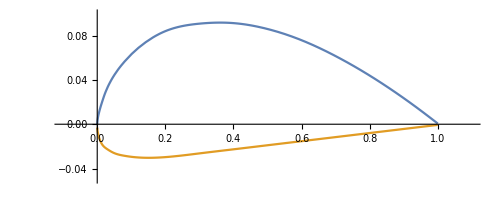

```mathematica
list=Import[StringTemplate["`dir`Airfoil Data/`l`.dat"][<|"dir"->ToString[NotebookDirectory[]],"l"->air|>]];
pos={};
neg={};
app=DeleteCases[DeleteDuplicates[Sort[list[[2;;-1]]]],{}];
Do[If[app[[i,2]]<0,AppendTo[neg,app[[i]]],AppendTo[pos,app[[i]]]],{i,1,Dimensions[app][[1]]}];
coords=Join[pos,Reverse[neg],{pos[[1]]}];
upper=Interpolation[pos,Method->"Spline"];
lower=Interpolation[neg,Method->"Spline"];
Plot[{upper[x],lower[x]},{x,0,1},AspectRatio->Automatic,PlotRange->{{-0.1,1.1},{-0.05,0.1}}]
regAirfoil=ImplicitRegion[lower[x]<y<upper[x]&&0<x<1,{x,y}];
{ymin,ymax}=MinMax[coords[[1;;-1,2]]];
Animate[seg={};
Do[AppendTo[seg,{coords[[i]],coords[[i+1]]}],{i,1,j}];
ListLinePlot[Flatten[seg,1],PlotRange->{{-0.05,1.05},{2ymin,2ymax}},AspectRatio->Automatic,PlotStyle->Red],
{j,1,Dimensions[coords][[1]]-1},AnimationRunning->False]
```

ElementMesh[{{0.,1.},{-0.0302546,0.0916266}},Automatic]

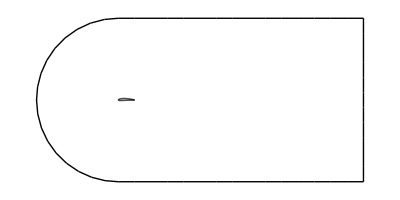

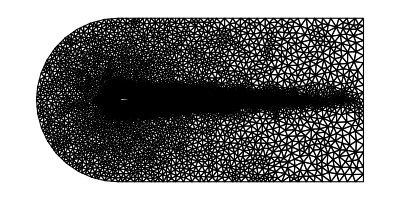

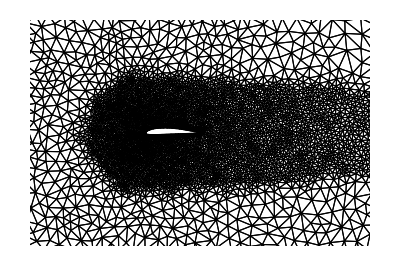

```mathematica
(* Mesh-Generation *)
(* choose the airfoil .dat file *)
airfoilDATA=Import[StringTemplate["`dir`Airfoil Data/`airfoil`.dat"][<|"dir"->ToString[NotebookDirectory[]],"airfoil"->air|>]];
airfoilClass=StringTemplate["`a``b`"][<|"a"->airfoilDATA[[1,1]],"b"->airfoilDATA[[1,2]]|>];
dataArray={a,b};
dataArray[[1]]=airfoilDATA[[2;;-1]];
dataArray[[2]]=Polygon[coords];
(* choose domain-size (1-length = 1-cord-length) *)
c=1;
H=10c; (* Domain height in cord-lengths *)
L=2*H;(* Domain Depth in cord-lengths *)
ℓ=2c; (* Refining region core dimension in cord-lengths *)
B=(L-H/2)*c;
Clear[x,𝓍];
𝓍rule=Solve[ℓ/(L-H/2+𝓍)==B/𝓍,𝓍];
𝓍=Abs[𝓍/.𝓍rule[[1]]];
region=ImplicitRegion[{(x^2+y^2≤(H/2)^2&& x≤0)||(x≥0&&y≤H/2&&y≥-H/2&&x≤L-H/2)},{x,y}];
Ω1=RegionUnion[Disk[{0,0},H/2],Rectangle[{0,-H/2},{L-H/2,H/2}]];
Ω2=dataArray[[2]];
Ω=RegionDifference[Ω1,Ω2];
bmesh1=ToBoundaryMesh[Ω1];
bmesh2=ToBoundaryMesh[Ω2]
ΩBoundaries=BoundaryElementMeshDifference[bmesh1,bmesh2];
ΩBoundaries["Wireframe"]
(* choose mesh-refining function *)
bigarea=c/10^2;
smallarea=bigarea/10;
meshrefine[vertices_,area_]:=area>bigarea;
f=Function[{vertices,area},area>bigarea(1+ Norm[Mean[vertices]])];
pred=((x^2+y^2<(ℓ/2)^2&&x≤0)||(-ℓ/(2B)x+ℓ/2>y&&ℓ/(2B)x-ℓ/2<y&&x>0));
g=Function[{vertices,area},Block[{x,y},{x,y}=Mean[vertices];If[pred,area>smallarea (1+ Norm[Mean[vertices]]),area>bigarea (1+ Norm[Mean[vertices]])]]];
mesh1=ToElementMesh[ΩBoundaries,MeshQualityGoal->"Maximal",MeshRefinementFunction->meshrefine,"MeshElementType"->QuadElement];
mesh1["Wireframe"];
mesh1["Wireframe"[PlotRange->{{-ℓ,2ℓ},{-ℓ,ℓ}}]];
mesh2=ToElementMesh[ΩBoundaries,MeshQualityGoal->"Maximal",MeshRefinementFunction->f];
mesh2["Wireframe"];
mesh2["Wireframe"[PlotRange->{{-ℓ,2ℓ},{-ℓ,ℓ}}]];
mesh3=ToElementMesh[ΩBoundaries,MeshQualityGoal->"Maximal",MeshRefinementFunction->g];
mesh3["Wireframe"]
mesh3["Wireframe"[PlotRange->{{-ℓ,2ℓ},{-ℓ,ℓ}}]]
{{mesh1["Wireframe"[PlotRange->{{-0.25,1.25},{-0.25,0.25}}]],
mesh2["Wireframe"[PlotRange->{{-0.25,1.25},{-0.25,0.25}}]],
mesh3["Wireframe"[PlotRange->{{-0.25,1.25},{-0.25,0.25}}]]},
{mesh1["Wireframe"[PlotRange->{{-0.08,.08},{-0.05,0.06}}]],
mesh2["Wireframe"[PlotRange->{{-0.08,.08},{-0.05,0.06}}]],
mesh3["Wireframe"[PlotRange->{{-0.08,.08},{-0.05,0.06}}]]},
{mesh1["Wireframe"[PlotRange->{{0.7,1.02},{-0.05,0.07}}]],
mesh2["Wireframe"[PlotRange->{{0.7,1.02},{-0.05,0.07}}]],
mesh3["Wireframe"[PlotRange->{{0.7,1.02},{-0.05,0.07}}]]}}//TableForm;
```

```mathematica
(* Snippet of data acquiring *)
```

```mathematica
Clear[coords,center,newcoords,combinations,vectors,sides,centermidvectors,ns]
```

```mathematica
(* Surface Vectors computing *)
Clear[coords]
(* input => cell coordinates *)
center=Mean[coords];
newcoords=Table[coords[[i]]-center,{i,1,3}];
combinations=Subsets[newcoords,{2}];
vectors=Table[combinations[[i,1]]-combinations[[i,2]],{i,1,3}];
sides=Subsets[newcoords,{2}];
centermidvectors=Table[Mean[sides[[i]]]-Mean[newcoords],{i,1,3}];
ns=Table[N[Norm[sides[[i]]]*(Mean[sides[[i]]]-Projection[centermidvectors[[i]],vectors[[i]]])/Norm[Mean[sides[[i]]]-Projection[centermidvectors[[i]],vectors[[i]]]]],{i,1,3}];
{xmin,xmax}={Min[Transpose[newcoords][[1]]],Max[Transpose[newcoords][[1]]]};
{ymin,ymax}={Min[Transpose[newcoords][[2]]],Max[Transpose[newcoords][[2]]]};
m=0.9;
Show[ListPlot[{Mean[newcoords]},PlotStyle->Red,PlotRange->{{xmin-m(xmax-xmin),xmax+m(xmax-xmin)},{ymin-m(ymax-ymin),ymax+m(ymax-ymin)}}],Graphics[{Green,Opacity[0.5],Triangle[newcoords]}],Graphics[{Red,Arrow[{Mean[newcoords],Mean[{newcoords[[1]],newcoords[[2]]}]}],Arrow[{Mean[newcoords],Mean[{newcoords[[1]],newcoords[[3]]}]}],Arrow[{Mean[newcoords],Mean[{newcoords[[2]],newcoords[[3]]}]}]}],Graphics[{Arrow[{Mean[sides[[1]]],Mean[sides[[1]]]+ns[[1]]}],Arrow[{Mean[sides[[2]]],Mean[sides[[2]]]+ns[[2]]}],Arrow[{Mean[sides[[3]]],Mean[sides[[3]]]+ns[[3]]}]}]]
```

```mathematica
M∞=3/10;
α=0;
γ=14/10;
c=1;
u∞=M∞*Cos[α];
v∞=M∞*Sin[α];
ρ∞=1;
a∞=1;
μ∞=1;
p∞=1/γ;
Rea=(ρ∞ c a∞)/(μ∞);
Cb1=1355/10^4;Cb2=622/10^3;σv=2/3;Cv1=71/10;Cv2=1;
Cw2=3/10;κ=41/100;Ct4=2;Ct3=11/10;Ct2=2;Ct1=1;Cw=Cb1/κ^2+(1+Cb2)/σv;
```

```mathematica
uv={u[t,x,y],v[t,x,y]}; μ=μ∞;ρxy=ρ[t,x,z];ℰ=En[t,x,y];pxy=γ-1(ℰ-ρxy(((uv[[1]])^2+(uv[[2]])^2)/2));
νtilda=νeddy[t,x,y];X=νtilda/(μ/ρxy);fv1=X^3/(X^3+Cv1^3);μt=ρxy*νtilda fv1;τxx=(μ+μt)/Rea(-2/3 Derivative[0,0,1][v][t,x,y]+4/3 Derivative[0,1,0][u][t,x,y]);
τyy=(μ+μt)/Rea(4/3 Derivative[0,0,1][v][t,x,y]-2/3 Derivative[0,1,0][u][t,x,y]);
τxy=(μ+μt)/Rea(Derivative[0,0,1][u][t,x,y]+Derivative[0,1,0][v][t,x,y]);
St=({{0, √((Derivative[0,0,1][u][t,x,y]-Derivative[0,1,0][v][t,x,y])^2)}, {√((-Derivative[0,0,1][u][t,x,y]+Derivative[0,1,0][v][t,x,y])^2), 0}}) ;
fv2=(1+X/Cv2)^-3;
fv3=((1+X fv1)(1-fv2))/Max[X,0.001];
Stilda=St fv (* Continue from this point onwards *)
```

{{0,fv √((u^(0,0,1)[t,x,y]-v^(0,1,0)[t,x,y])^2)},{fv √((-u^(0,0,1)[t,x,y]+v^(0,1,0)[t,x,y])^2),0}}

```mathematica
U={ρxy,ρxy uv[[1]],ρxy uv[[2]], ℰ};
F={ρxy uv[[1]],ρxy uv[[1]]^2+ρxy,ρxy uv[[1]] uv[[2]],uv[[1]](ℰ+pxy)};
G={ρxy uv[[2]],ρxy uv[[1]] uv[[2]],ρxy uv[[2]]^2+ρxy,uv[[2]](ℰ+pxy)};
Fv={0,τxx,τxy,τxx uv[[1]]+τxy uv[[2]]};
Gv={0,τxy,τyy,τxy uv[[1]]+τyy uv[[2]]};
S={0,0,0,0};
SA=D[νtilda,t]+uv[[1]]*D[νtilda,x]+uv[[2]]*D[νtilda,y];
SALeft=Cb1/Rea Stilda νtilda+(∇_{x,y} .((μ/ρxy+νtilda)∇_{x,y} νtilda)+Cb2(∇_{x,y} νtilda)^2)/(σ*Rea)-1/Rea(Cw1 fw)(νtilda/d)^2;
NS=Table[D[U[[i]],t]+D[F[[i]],x]+D[G[[i]],y],{i,1,4}];
NSLeft=Table[D[Fv[[i]],x]+D[Gv[[i]],y]+S[[i]],{i,1,4}];
MatrixForm[NS];
MatrixForm[NSLeft];
NSOperator=NS==NSLeft;
MatrixForm[NSOperator];
```

```mathematica
bcs= {DirichletCondition[{uv[[1]]==u∞,uv[[2]]==v∞,ρxy==ρ∞,a[t,x,y]==a∞,pxy==p∞,ℰ==(p∞)/(γ-1)+(ρ∞)/2((u∞)^2+(v∞)^2)},x^2+y^2==(H/2)^2&&x<0](* FS-conditions *),
DirichletCondition[{uv[[1]]==0,uv[[2]]==0,νtilda==0},{x,y}∈dataArray[[2]]](* no-slip *),
DirichletCondition[{uv[[1]]==u∞,uv[[2]]==v∞,ρxy==ρ∞,a[t,x,y]==a∞,pxy==p∞,ℰ==(p∞)/(γ-1)+(ρ∞)/2((u∞)^2+(v∞)^2)},(y==-H/2||y==H/2||x==L-H/2)](* Far-Boundary *)};
ic={DirichletCondition[{uv[[1]]==u∞,uv[[2]]==v∞,ρxy==ρ∞,a[t,x,y]==a∞,pxy==p∞,ℰ==(p∞)/(γ-1)+(ρ∞)/2((u∞)^2+(v∞)^2)},t==0&&{x,y}∈Ω]}
```

```mathematica
?DirichletCondition
```

```mathematica
d[x_,y_]:=RegionDistanceFunction[regAirfoil][x_,y_]
```

SetDelayed::write: Tag RegionDistanceFunction in RegionDistanceFunction[ImplicitRegion[{x,y}<InterpolatingFunction[{{0.,1.}},{5,7,0,{61},{4},0,0,0,0,Automatic,«3»},{{0.,0.0005,0.001,0.002,0.004,0.008,0.012,0.02,0.03,0.04,«51»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«52»},{0.,0.002339,0.0037271,0.0058025,0.0089238,0.013735,0.0178581,0.0253735,0.0330215,0.0391283,«51»}},{Automatic}]&&{x,y}>InterpolatingFunction[{{0.0005,0.99}},«3»,{Automatic}],{x,y}]][x_,y_] is Protected.

$Failed

```mathematica
Plot3D[RegionDistance[dataArray[[2]],{x,y}],{x,y}∈RegionUnion[Ω],AspectRatio->Automatic]
```

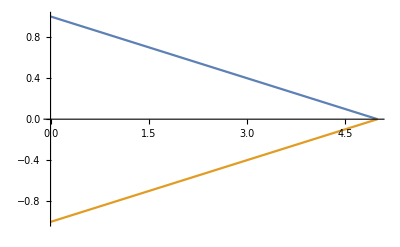

```mathematica
Plot[{-ℓ/(2B)x+ℓ/2,ℓ/(2B)x-ℓ/2},{x,0,B}]
```